```mathematica
Qb = a*Et^b
```

a Et^b

```mathematica
Subscript[σ, I]= Sqrt[((Subscript[σ, oI])^2 + (Subscript[a, I]*Qb*Et)^2)]
```

√(a^2 Et^(2+2 b) a_ⅈ^2+σ_oI^2)

```mathematica
Subscript[σ, H]= Sqrt[((Subscript[σ, oH])^2 + (Subscript[a, H]*Et)^2)]
```

√(Et^2 a_H^2+σ_oH^2)

```mathematica
fc = P*Abs[Et]*Exp[-(Et - Er)^2/sa]*Exp[-(Er*Qb-Et*Q)^2/sc]
```

ⅇ^(-(-Er+Et)^2/sa-((a Er Et^b-Et Q)^2)/sc) P Abs[Et]

```mathematica
fa = ((2*scale*(Et -Er))/sa) + ((2*(Er*Qb-Et*Q))/sc)
```

(2 (a Er Et^b-Et Q))/sc+(2 (-Er+Et) scale)/sa

```mathematica
fb = (1/sb) + (scale^2/sa) + (1/sc)
```

1/sb+1/sc+scale^2/sa

```mathematica
fd = fc*Exp[fa^2/(4*fb)]*(Sqrt[Pi]/Sqrt[fb])*(1/α)*Exp[-α*Er]
```

(ⅇ^(-(-Er+Et)^2/sa-((a Er Et^b-Et Q)^2)/sc+(((2 (a Er Et^b-Et Q))/sc+(2 (-Er+Et) scale)/sa)^2)/(4 (1/sb+1/sc+scale^2/sa))-Er α) P √π Abs[Et])/(√(1/sb+1/sc+scale^2/sa) α)

```mathematica
Qd = Integrate[fd,{Er,0,Infinity}]
```

ConditionalExpression[(ⅇ^((-4 a^2 Et^(2+2 b)-4 Et^2 Q^2-4 Et (sb+sc+Q sb scale) α+(sa (sb+sc)+sb sc scale^2) α^2+4 a Et^(1+b) (2 Et Q-(Q sa+sb scale+Q sb scale^2) α))/(4 (sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2)))) P π Abs[Et] (1+Erf[(2 Et (sb+sc+Q sb scale)+2 a Et^(1+b) (sb scale+Q (sa+sb scale^2))-(sa (sb+sc)+sb sc scale^2) α)/(2 (sa (sb+sc)+sb sc scale^2) √((sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2))/(sa (sb+sc)+sb sc scale^2)))]))/(2 √(1/sb+1/sc+scale^2/sa) √((sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2))/(sa (sb+sc)+sb sc scale^2)) α),(Re[(sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2))/(sa (sb+sc)+sb sc scale^2)]≥0&&Re[(2 Et (sb+sc+Q sb scale)+2 a Et^(1+b) (sb scale+Q (sa+sb scale^2))-(sa (sb+sc)+sb sc scale^2) α)/(sa (sb+sc)+sb sc scale^2)]<0)||Re[(sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2))/(sa (sb+sc)+sb sc scale^2)]>0]

```mathematica
Qd_new = Simplify[Qd,{scale ∈ Reals, scale > 0, sa ∈ Reals, sa > 0, sb ∈ Reals, sb>0, sc ∈ Reals, sc ≥ 0, a ∈ Reals, a > 0, b ∈ Reals, b >0, Et ∈ Reals, Et>0, Q ∈ Reals, α ∈ Reals, α > 0}]
```

ConditionalExpression[(ⅇ^((-4 a^2 Et^(2+2 b)-4 Et^2 Q^2-4 Et (sb+sc+Q sb scale) α+(sa (sb+sc)+sb sc scale^2) α^2+4 a Et^(1+b) (2 Et Q-(Q sa+sb scale+Q sb scale^2) α))/(4 (sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2)))) Et P π (1+Erf[(2 Et (sb+sc+Q sb scale)+2 a Et^(1+b) (sb scale+Q (sa+sb scale^2))-(sa (sb+sc)+sb sc scale^2) α)/(2 √((sa (sb+sc)+sb sc scale^2) (sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2))))]))/(2 √((sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2))/(sa sb sc)) α),2 Et (a Et^b Q sa+sb+sc+a Et^b sb scale+Q sb scale+a Et^b Q sb scale^2)<(sa sb+sa sc+sb sc scale^2) α||a^2 Et^(2 b) sa+sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) sb scale^2>0]

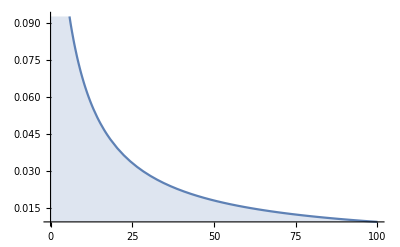

```mathematica
Plot[Simplify[1/(x+y),{y==5}],{x,0,100},Filling->Bottom]
```

```mathematica
Plot[Simplify[Qd,{sa==0.5,sb==0.5,sc==0.5,Et==10.0,a==0.16,b==0.18,scale==1.0, P==1, α==(1/18.0)}],{Q,-0.1,0.5},Filling->Axis,AxesLabel->{"ionization yield (10 keV)",PDF}]
```

$Aborted

```mathematica
Simplify[Qd,{sa==0.5,sb==0.5,sc==0.5,Et==10.0,a==0.16,b==0.18,scale==1.0, P==1, α==(1/18.0)}]
```

0.59843 ⅇ^((36.9166-76.8748 Q) Q) (1.+Erf[11.329+7.51389 Q])

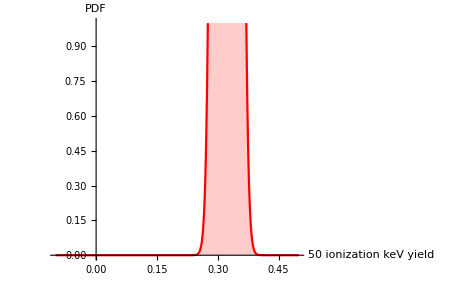

```mathematica
Plot[Simplify[Qd,{sa==0.5,sb==0.5,sc==0.5,Et==50.0,a==0.16,b==0.18,scale==1.0, P==1, α==(1/18.0)}],{Q,-0.1,0.5},Filling->Axis,PlotStyle->Red,PlotRange->{{-0.1,0.5},{0,10.0}},AxesLabel->{"ionization yield (50 keV)",PDF}]
```

```mathematica
Integrate[Simplify[Q*Qd,{sa==0.5,sb==0.5,sc==0.5,a==0.16,b==0.18,scale==1.0, P==1, α==(1/18.0)}],{Q,-Infinity,Infinity}]
```

∫_(-∞)^∞ ((11.5429 ⅇ^(-(-0.0226056+Et^(59/25)+Et^1.18 (0.173611+0.347222 Q)-12.5 Et^2.18 Q+39.0625 Et^2 Q^2+1.08507 Et (2.+Q))/(39.0625+6.25 Et^0.18+Et^(9/25))) Q Abs[Et] (1+Erf[(-0.0277778+Et^1.18 (0.106667+0.213333 Q)+0.666667 Et (2.+Q))/(√(1.33333+0.213333 Et^0.18+0.0341333 Et^0.36))]))/(√(1.33333+0.213333 Et^0.18+0.0341333 Et^0.36)))ⅆQ

```mathematica
Integrate[Simplify[Q^2*Qd,{sa==0.5,sb==0.5,sc==0.5,a==0.16,b==0.18,scale==1.0, P==1, α==(1/18.0)}],{Q,-Infinity,Infinity}]
```

∫_(-∞)^∞ ((11.5429 ⅇ^(-(-0.0226056+Et^(59/25)+Et^1.18 (0.173611+0.347222 Q)-12.5 Et^2.18 Q+39.0625 Et^2 Q^2+1.08507 Et (2.+Q))/(39.0625+6.25 Et^0.18+Et^(9/25))) Q^2 Abs[Et] (1+Erf[(-0.0277778+Et^1.18 (0.106667+0.213333 Q)+0.666667 Et (2.+Q))/(√(1.33333+0.213333 Et^0.18+0.0341333 Et^0.36))]))/(√(1.33333+0.213333 Et^0.18+0.0341333 Et^0.36)))ⅆQ

```mathematica
Simplify[Qd,{scale ∈ Reals, scale > 0, sa ∈ Reals, sa > 0, sb ∈ Reals, sb>0, sc ∈ Reals, sc ≥ 0, a ∈ Reals, a > 0, a< 1, b ∈ Reals, b >0, b<1, Et ∈ Reals, Et>0, Q ∈ Reals, α ∈ Reals, α > 0}]
```

ConditionalExpression[(ⅇ^((-4 a^2 Et^(2+2 b)-4 Et^2 Q^2-4 Et (sb+sc+Q sb scale) α+(sa (sb+sc)+sb sc scale^2) α^2+4 a Et^(1+b) (2 Et Q-(Q sa+sb scale+Q sb scale^2) α))/(4 (sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2)))) Et P π (1+Erf[(2 Et (sb+sc+Q sb scale)+2 a Et^(1+b) (sb scale+Q (sa+sb scale^2))-(sa (sb+sc)+sb sc scale^2) α)/(2 √((sa (sb+sc)+sb sc scale^2) (sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2))))]))/(2 √((sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) (sa+sb scale^2))/(sa sb sc)) α),2 Et (a Et^b Q sa+sb+sc+a Et^b sb scale+Q sb scale+a Et^b Q sb scale^2)<(sa sb+sa sc+sb sc scale^2) α||a^2 Et^(2 b) sa+sb+sc+2 a Et^b sb scale+a^2 Et^(2 b) sb scale^2>0]